# Conway’s IRIS

```mathematica
DynamicModule[{a={-0.5,-0.5},b={0.5,-0.5},c={0,0.5},a1,a2,b1,b2,c1,c2,ab,bc,ca,aa1,aa2,bb1,bb2,cc1,cc2,tri,i,ir,or,arc1,arc2,arc3,arc4,arc5,arc6,vecArg,minorArc},
vecArg[v_]:=Arg[Complex@@v];
minorArc[{p1_,p2_},q_]:=With[{θ1=vecArg[p1-q],θ2=vecArg[p2-q],r=Norm[p1-q]},Circle[q,r,If[Abs[θ1-θ2]>π,Mod[{θ1,θ2},2π],{θ1,θ2}]]];LocatorPane[Dynamic[{a,b,c}],Dynamic[tri={a,b,c};i=TriangleCenter[tri,"Incenter"];ir=TriangleMeasurement[tri,"Inradius"];ab={a,b};bc={b,c};ca={c,a};a1=a+Norm[b-c]Normalize[a-b];a2=a+Norm[b-c]Normalize[a-c];b1=b+Norm[c-a]Normalize[b-c];b2=b+Norm[c-a]Normalize[b-a];c1=c+Norm[a-b]Normalize[c-a];c2=c+Norm[a-b]Normalize[c-b];or=Norm[a1-i];
aa1={a,a1};aa2={a,a2};bb1={b,b1};bb2={b,b2};cc1={c,c1};cc2={c,c2};arc1=minorArc[{a1,a2},a];arc2=minorArc[{a2,b1},c];arc3=minorArc[{b1,b2},b];arc4=minorArc[{b2,c1},a];arc5=minorArc[{c1,c2},c];arc6=minorArc[{c2,a1},b];Graphics[{{Gray,Circle[i,ir],Circle[i,or]},{Purple,arc1,arc2,arc3,arc4,arc5,arc6},Thick,Red,Line[{ab,cc1,cc2}],Green,Line[{bc,aa1,aa2}],Blue,Line[{ca,bb1,bb2}],PointSize[Large],Magenta,Point[{a,b,c}],PointSize[Medium],Pink,Point[{a1,a2,b1,b2,c1,c2,i}]},PlotRange->3,ImageSize->Large]],Appearance->None]]
```

```mathematica
pts={{-1.618033988749895,-0.5},{-1.4510565162951536,-1.0877852522924731},{-1.,-1.5}};
CircularArcThrough[pts]
```

Circle[{-0.5,-0.5},1.11803,{-2.84188,-2.1588}]

```mathematica
CircularArcThrough[{{1,0},{0,1}},{0.5,0.5},1/(√2)]
```

CircularArcThrough[{{1,0},{0,1}},{0.5,0.5},1/(√2)]

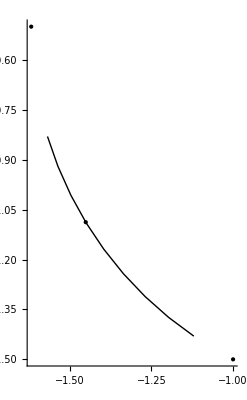

```mathematica
Graphics[{CircularArcThrough[pts],Point[pts]},Axes->{True,True},PlotRange->2]
```

### 由此发现CircularArcThrough在14版中还存在一些问题

```mathematica
vecArg[v_]:=Arg[Complex@@v];
arcThrough[{p1_,p2_},q_]:=With[{θ1=vecArg[p1-q],θ2=vecArg[p2-q]},Circle[q,Norm[p1-q],{θ1,If[θ1>θ2,θ2+2π,θ2]}]]
arcThrough2[{p1_,p2_},q_]:=With[{θ1=vecArg[p1-q],θ2=vecArg[p2-q]},Circle[q,Norm[p1-q],{θ1,θ2}]]
```

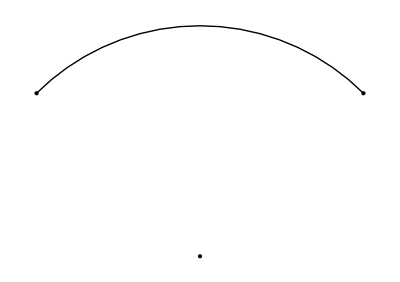

```mathematica
{a,b,c}={{-0.5,0.5},{0.5,0.5},{0,0}};
Graphics[{arcThrough2[{a,b},c],Point[{a,b,c}]},PlotRange->1]
```

### 关于圆弧的问题

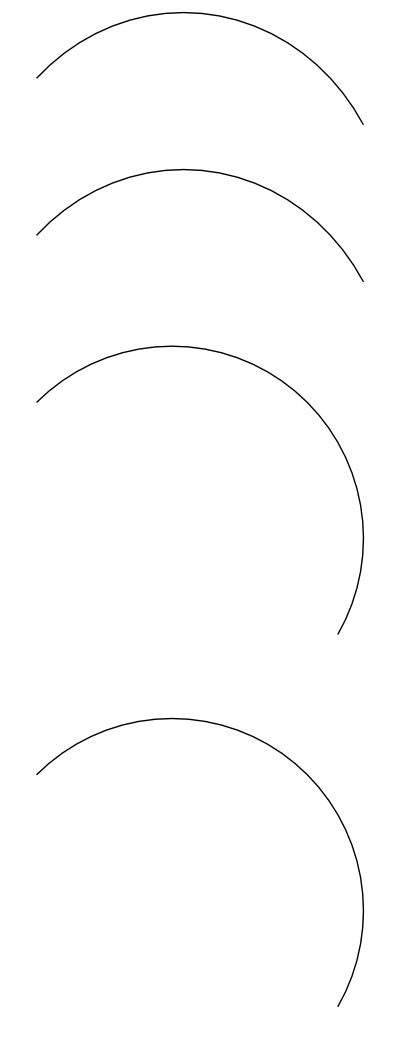

```mathematica
GraphicsColumn[
{Graphics[Circle[{0,0},1,{3Pi/4,Pi/6}]],Graphics[Circle[{0,0},1,{Pi/6,3Pi/4}]],Graphics[Circle[{0,0},1,{-Pi/6,3Pi/4}]],Graphics[Circle[{0,0},1,{3Pi/4,-Pi/6}]]}]
```

### 注意的此处使用Mod的技巧

```mathematica
θ=Arg[Complex@@{-1,-1}]
If[θ<0,θ+2π]
```

-(3 π)/4

(5 π)/4

```mathematica
Mod[θ,2π]
```

(5 π)/4